```mathematica
(*This code generates the phase plots in the x, H, Ωm coordinate system*)
Clear[α1,P2,ex,eH,eΩm,Eqx,EqH,EqΩm,x,H,Ωm];
(*Defining the dynamical system which was obtained manually*)
Eqx[N_] := x[N]/2 (4P2+x[N]^(2/P2)(1-4P2+(6H[N]^(2-4P2)(Ωm[N]-1))/(24^P2 x[N]^2 α1 (P2-1))));
EqH[N_] := H[N](x[N]^(2/P2)-1);
EqΩm [N_]:= -Ωm[N](1+2x[N]^(2/P2));
(*Defining the value of the parameters*)
P2=2;
α1=1/2;
(*Simplifying the dynamical system for plotting*)
ex = Eqx[N]/.x_[N]-> x;
eH= EqH[N]/.x_[N]-> x;
eΩm = EqΩm[N]/.x_[N]->x;
(*Defining the coordinates of the fixed points*)
x2 = (4P2/(4P2-1))^(P2/2);
N[H3 = (24^P2 α1 (P2-1)/6)^(1/(2-4P2))]

(*Plotting the fixed points and their labels*)(*Note that certain points needed to be included only for specific values of the parameters*)
cp = Graphics3D[{PointSize[0.02], (*Point[{x2,0,0}],*) Point[{1,H3,0}]}];
labelsf = Graphics3D[{(*Text[Style["C_2",20],{x2,0,0},{-1,-1}],*) Text[Style["C_1",20],{1,H3,0},{0,1}]}];
(*Generating the stream plot*)
st = StreamPlot3D[{ex,eH,eΩm},{x,0,2},{H,0,1},{Ωm,0,1},StreamMarkers->"Arrow",StreamPoints->30,AxesLabel->{x,H,Subscript[Ω, m]},AxesStyle->Black,StreamColorFunction->None];
Show[st,cp,labelsf]
```

0.524558

-Graphics3D-

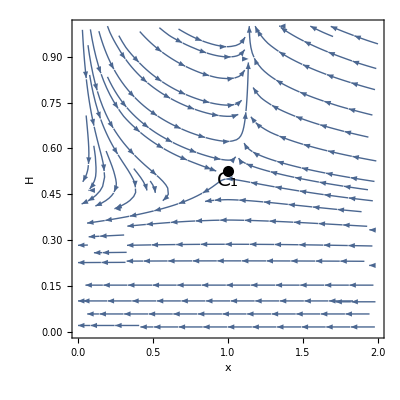

```mathematica
(*This part of the code generates the stream plot in the Ωm = 0 plane*)
Clear[x,H,Ωm];
Ωm = 0;
(*Getting a phase plot in the Ωm = 0 plane*)
st2 = StreamPlot[{ex,eH},{x,0,2},{H,0,1},FrameLabel->{x,H},Axes->False,FrameStyle->Black,StreamColorFunction->None,RotateLabel->False];
(*Plotting the fixed points and their labels*)
cp2 = Graphics[{PointSize[0.02],(*Point[{x2,0}],*) Point[{1,H3}]}];
labelsf2 = Graphics[{(*Text[Style["C_2",20],{x2,0},{-1.5,0}],*) Text[Style["C_1",20],{1,H3},{0,1.5}]}];
Show[st2,cp2,labelsf2]
```